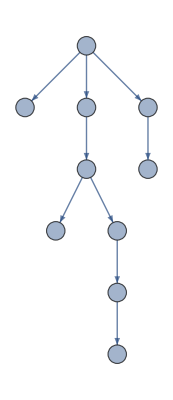

```mathematica
Edges = {5->1, 5->2, 5->6, 6->4, 3->7, 3->8,2->3, 9->10,8->9};
graph = Graph[Edges, GraphLayout->{"LayeredEmbedding", "RootVertex"-> 5}, VertexSize->0.3, VertexLabels->Placed["Name",Center]]
```

```mathematica
pred = {5,5,2,6,0,5,3,3,8,9};
depth = {1,1,2,2,0,1,3,3,4,5};
thread = {2,3,4, 10,1,9,5,6,7,8};
dinast = {2,3,7,5,1,4,8,9,10,6};
```

Task 1
The only chain in the tree

```mathematica
Chain[vertex_]:=NestWhileList[pred[[#]]&,vertex,pred[[#]]≠ 0&];
Chain[5]
Chain[4]
Chain[10]
```

{5}

{4,6,5}

{10,9,8,3,2,5}

Task 2
Find the path between two vertices

```mathematica
PathBetweenVertices[start_,end_]:=Module[
{result = List[], chainStart, chainEnd, intersect},
chainStart = Chain[start];
chainEnd = Chain[end];
intersect = Intersection[chainEnd, chainStart];
If[ContainsAll[intersect,{end}],
result=Complement[chainStart, chainEnd];
PrependTo[result,end];
Return@result;
];
If[ContainsAll[intersect,{start}],
result=Complement[chainEnd, chainStart];
PrependTo[result,start];
Return@result;
];
result = Complement[chainEnd, chainStart];
result = Prepend[result, pred[[result[[1]]]]];
PrependTo[result, #]&/@Reverse[Complement[chainStart, chainEnd]];
Return@result;
];
PathBetweenVertices[7,10]
```

{7,3,8,9,10}

Task 3
finding subtree

```mathematica
FindSubtree[vertex_]:=NestWhileList[dinast[[#]]&,vertex,depth[[dinast[[#]]]]> depth[[vertex]]&];
FindSubtree[6]
```

{6,4}

Task 4
search of chain

find all leaves

```mathematica
GetAllLeaves1[graph_]:=Select[depth[[#]]≥ depth[[dinast[[#]]]]&]@dinast;
GetAllLeaves2[graph_]:= Select[# ≠ pred[[dinast[[#]]]]&]@dinast;
GetAllLeaves1[graph]
GetAllLeaves2[graph]
```

{7,1,4,10}

{7,1,4,10}